# Length contraction

-Graphics-

l'=x'_2−x'_1=γ(x_2−v t_2)−γ(x_1−v t_1)=−γv(t_2−t_1)_0+γ(x_2−x_1)_l=γl
⇒l=1/γ l'

## Example

### Speed of light

```mathematica
c=299792458;
```

### Relative velocity between inertial reference frames

```mathematica
v=0.8c;
```

### Ratio of relative velocity v to the speed of light c

```mathematica
β[𝓋_]=𝓋/c;
```

### Lorentz factor

```mathematica
γ[𝓋_]=1/(√(1-β[𝓋]^2));
```

### Proper length

```mathematica
l'=1;
```

### Length

```mathematica
l[𝓋_]=1/γ[𝓋] l';
```

```mathematica
l[v]
```

0.6

## Plot

```mathematica
Plot1=Plot[l[𝓋],{𝓋,0,c},FrameLabel->{"v (m/s)","Length (m)"},PlotLegends->"Expressions",Frame-> True,GridLines->Automatic];
```

```mathematica
Plot2=ListPlot[{{v,l[v]}},MeshStyle->Red,PlotMarkers->{Automatic,Medium}];
```

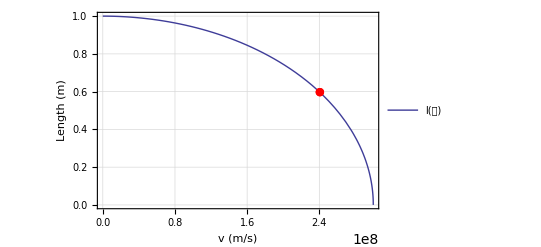

```mathematica
Show[Plot1,Plot2]
```